Program calculating rate constants for van der Waals interaction for arbitrary boundary conditions at short range 
Everything in units of R_vdw and E_vdw (characteristic length and energy for van der Waals interaction)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Oem\Desktop\Dipoles final

Parameters:
Lmax - maximal value of angular momentum L
xi - minimal value of r in the grid
nptl - number of points to tabulate the wavelenght
npt - numeber of point per de Broglie wavelenght in the grid 
energ - energy of particles
epsi - small number used to determine initial point of integration
epsf - small number used to determine final point of integration
dxf - step used to determine the final point of integration

Table of parametrs

```mathematica
Lmin=0;Lmax=32;nptl=500;npt=30;epsf=10^-12;epsi=10^-4;dxf=10;
```

```mathematica
KtoEh=3.1668153 10^(-6);
HztoEh=1.519829 10^(-16);
massunit=1.661 10^(-24)/(9.110 10^(-28));
μ=81.25 massunit; 
Debye=0.393456;
d=9/(137*2);
m = 9.18 BohrM;
```

```mathematica
C6=2277;
```

```mathematica
R6=(2 μ C6)^(1/4);E6=1/(2 μ R6^2);
```

```mathematica
abar=(Pi/8)/Gamma[5/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;
C3=2d^2;R3=2 μ C3/R6;E3=(1/(2μ (R6 R3)^2))/E6;
β=R3
```

3.9669

```mathematica
xf=100;
```

```mathematica
freq=30000; 
freqz=0.1 freq;
ω=2 π freq HztoEh; ωz=2 π freqz HztoEh;aHO=(1/Sqrt[μ ω])/R6; aHOz=(1/Sqrt[μ ωz])/R6;
α=(1/aHO)^4;
αz=(1/aHOz)^4;
Ω=2 Sqrt[α];
Ωz=2 Sqrt[αz];
```

Potentials

```mathematica
Vho[l1_,ml1_,l2_,ml2_]:= (If[l1==l2,1,0]If[ml1==ml2,1,0]-(1-αz/α)If[ml1==ml2,1,0]/3((-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1] 2 ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}] + If[l1==l2,1,0]));
Vedd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];(*Dodać symbol wignera*)
Vmdd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];
Vvdw[l1_,ml1_,l2_,ml2_]:= -If[l1==l2,1,0]If[ml1==ml2,1,0];
```

```mathematica
Veddtab=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vmddtab=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vvdwtab=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vhotab=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vcftab = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,0,Lmax},{l2,0,Lmax}]]];
Veddtab2=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vmddtab2=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vvdwtab2=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vhotab2=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vcftab2 = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,1,Lmax},{l2,1,Lmax}]]];
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
Vhotable[x_]:=N[(Table[Vhotab[[l1/2+1,l2/2+1]],{l1,0,Lmax},{l2,0,Lmax}])/.{r->x}];
```

Table of channels

```mathematica
TabCh={};Do[AppendTo[TabCh,{l(*,m*)}],{l,Lmin,Lmax}(*,{m,-l,l}*)];Nch=Length[TabCh];Id=IdentityMatrix[Lmax+1];Nch
```

33

Spherical Bessel functions

```mathematica
jl[l_,x_]:=Sqrt[Pi/(2x)]BesselJ[l+1/2,x];nl[l_,x_]:=(-1)^(l+1) Sqrt[Pi/(2x)]BesselJ[-l-1/2,x]
```

Matrix containg potential

```mathematica
V[r_]:=1/r^2 Vcftab + 1/r^6 Vvdwtab +β/r^3 Veddtab;
```

```mathematica
Length[V[1][[1]]]
```

33

Adiabatic potentials (diagonalized V[r]) + van der Waals potential

Take::take: Cannot take positions 1 through 16 in Eigenvalues[V2[0.500054]].

Take::take: Cannot take positions 1 through 16 in Eigenvalues[V2[0.557156]].

Take::take: Cannot take positions 1 through 16 in Eigenvalues[V2[0.620778]].

General::stop: Further output of Take::take will be suppressed during this calculation.

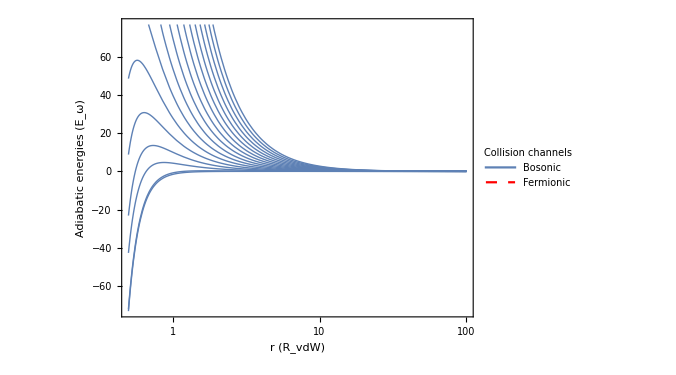

```mathematica
LogLinearPlot[{(Take[Sort[Eigenvalues[V[x]]],Lmax/2+1]),(Take[Sort[Eigenvalues[V2[x]]],Lmax/2])},{x,0.5,xf},
PlotRange->Automatic,AxesOrigin->{0.5,0},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},PlotLegends->Placed[LineLegend[{Style["Bosonic",FontFamily->"Times",FontWeight->Bold],Style["Fermionic",FontFamily->"Times",FontWeight->Bold]}, LegendLabel->Style["Collision channels",FontSize->14, FontFamily->"Times",FontWeight->Bold],LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMargins->5],{Left,Top}],FrameLabel->{Style["r (R_vdW)",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["Adiabatic energies (E_ω)",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
N[abar]*4
```

1.91196

Short range solution for van der Waals potential, with the short range phase "phi"

```mathematica
sol0[r_,A_,B_]=A Sqrt[r]BesselJ[1/4,1/(2 r^2)]+B Sqrt[r] BesselY[1/4,1/(2 r^2)];
```

```mathematica
ash[phi_]:=abar (1+Tan[phi])
```

```mathematica
as[y_,s_]:=abar(s+y(1+(1-s)^2)/(ⅈ+y(1-s)));
ap[y_,s_,k_]:=-2 abar1  (k abar)^2  (y+ⅈ(s-1))/(y s+ⅈ(s-2))
```

Table of short range solutions

```mathematica
Psi0[r_,A_,B_]:=Table[If[n1==n2,sol0[r,A,B],0] ,{n1,1,Nch},{n2,1,Nch}]
```

Subroutine performing outward integration using renormalized Numerov method
It takes Psi0 as an initial condition

Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
phi - short-range phase

```mathematica
evolNumOut[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,A_?NumericQ,B_?NumericQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,Ro,Rprod},

nodes=0;

Rout[n0]=Psi0[xt[[n0+1]],A,B].Inverse[Psi0[xt[[n0]],A,B]];
h=xt[[n0+1]]-xt[[n0]];
n=n0+1;

While[n<=nf,
h0=h;
h=xt[[n+1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n-2]]).Inverse[Rout[n-1].Rout[n-2]]);,

Abs[h]<0.75 Abs[h0],
Qt=en Id-V[(xt[[n]]+xt[[n-1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n-1]]).Inverse[Rout[n-1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n-1]]).Inverse[Rout[n-1]]);
];
n++;
];
Ro=Rout[nf];
Rprod=Inverse[Rout[n0]];Do[Rprod=Rprod.Inverse[Rout[n]],{n,n0+1,nf-1}];
Clear[W,n,Rinv,h,h0,Qt];
If[cl==1,Clear[Rout]];
{Ro,Rprod}]
```

Subroutine calculating K matrix

Parameters:
en -  the energy
A,B - constants determining boundary conditions at short range 

Output:
K matrix

```mathematica
KMatrix[en_?NumericQ,A_?NumericQ,B_?NumericQ]:=
Module[{J1,J2,N1,N2,Rn,K,r1,r2,kv,n1,n2,Rprod,R},
R=evolNumOut[en,1,nstep-1,A,B,1];
Rn=R[[1]];
kv=Sqrt[en];
r1=xt[[nstep-1]];
r2=xt[[nstep]];
J1=Table[If[n1==n2, kv r1 jl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
J2=Table[If[n1==n2,kv r2 jl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
N1=Table[If[n1==n2,kv r1 nl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
N2=Table[If[n1==n2,kv r2 nl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
K=-Inverse[Rn.N1-N2].(J2-Rn.J1);
K];
```

Subroutine calculating K and T matrices

Parameters:
en -  the energy
A,B - constants determining boundary conditions at short range 

Output:
K matrix
T matrix

```mathematica
KCTMatrix[en_?NumericQ,A_?NumericQ,B_?NumericQ]:=
Module[{J1,J2,N1,N2,Rn,K,r1,r2,kv,n1,n2,Rprod,R,W,T},
R=evolNumOut[en,1,nstep-1,A,B,1];
Rn=R[[1]];
Rprod=R[[2]];
kv=Sqrt[en];
r1=xt[[nstep-1]];
r2=xt[[nstep]];
J1=Table[If[n1==n2, kv r1 jl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
J2=Table[If[n1==n2,kv r2 jl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
N1=Table[If[n1==n2,kv r1 nl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
N2=Table[If[n1==n2,kv r2 nl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
K=-Inverse[Rn.N1-N2].(J2-Rn.J1);
W=Rprod.(J1+N1.K).Inverse[Id-ⅈ K];
R=ConjugateTranspose[W].W;
W=Inverse[Id-ⅈ K];
T=W.K/ Sqrt[en];
{T,K,Re[Tr[R]]}];
```

```mathematica
yy=0;ss=4.;
```

```mathematica
aS=as[yy,ss]
```

1.91196+0. ⅈ

```mathematica
aP=ap[yy,ss,Sqrt[en]]
```

-3.48683×10^-8+0. ⅈ

```mathematica
phi=φ/.Solve[aS==ash[φ],φ][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.24905

```mathematica
abar=(Pi/8)/Gamma[5/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;
```

energies

```mathematica
en0=0.0001;enf=100.;de=(Log[enf]-Log[en0])/50;
```

```mathematica
TabEn=Table[Exp[ee],{ee,Log[en0],Log[enf],de}]
```

{0.0001,0.000131826,0.00017378,0.000229087,0.000301995,0.000398107,0.000524807,0.000691831,0.000912011,0.00120226,0.00158489,0.0020893,0.00275423,0.00363078,0.0047863,0.00630957,0.00831764,0.0109648,0.0144544,0.0190546,0.0251189,0.0331131,0.0436516,0.057544,0.0758578,0.1,0.131826,0.17378,0.229087,0.301995,0.398107,0.524807,0.691831,0.912011,1.20226,1.58489,2.0893,2.75423,3.63078,4.7863,6.30957,8.31764,10.9648,14.4544,19.0546,25.1189,33.1131,43.6516,57.544,75.8578,100.}

loop

```mathematica
Elastic={};Inelastic={}; Sections={};
Print["Progress:"];
Print[ProgressIndicator[Dynamic[counter],{1,Length[TabEn]}]];
Do[en=TabEn[[i]];
counter=i;
(*Print["en = ",en];*)

xi=0.25;
(*Determines the final point of integration*)
xf=100;

(* Subroutine determining steps *)
Module[{eig,h,dbl,n,pxi,pxf,dp,x,p,tab},

pxi=Log[xi ];
pxf=Log[xf +dxf];
dp=(pxf-pxi)/nptl;
tab=Table[x=Exp[p];eig=Eigenvalues[V[x]];{x,Min[2Pi/Sqrt[Abs[en-eig]]]},{p,pxi,pxf,dp}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,


AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
];
(*Print["nstep = ",nstep];*)
QT=Table[en Id-V[xt[[n]]],{n,1,Length[xt]}];
Kmatr=KMatrix[en,Sin[phi],Cos[phi]];
Smatr=(Id+ⅈ Kmatr).Inverse[Id-ⅈ Kmatr];
S0 = N[Smatr[[1,1]]];
a0 = 1/(ⅈ Sqrt[en])(1-S0)/(1+S0);

(*totinelS=Pi Sum[1-Abs[Smatr[[n1,n1]]]^2,{n1,1,1}]/en;
totelS=Pi Sum[Abs[1-Smatr[[n1,n1]]]^2,{n1,1,1}]/en;*)

totInEl= Sum[(2TabCh[[n1,1]]+1)(1-Abs[Smatr[[n1,n1]]]^2),{n1,1,Nch}];
totEl=  Sum[(2TabCh[[n1,1]]+1)Abs[1-Smatr[[n1,n1]]]^2,{n1,1,Nch}];

AppendTo[Elastic,{en,totEl}];
AppendTo[Inelastic,{en,totInEl}];
AppendTo[Sections,{en,a0}];

Clear[xt,QT];
,{i,1,Length[TabEn]}
]
```

Progress:

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00569536,0.,0.000174124,0.,4.87793×10^-6,0.,2.58073×10^-7,0.,1.6179×10^-8,0.,«23»},{0.,-0.0158406,0.,0.000335964,0.,7.96379×10^-6,0.,3.73024×10^-7,0.,2.13182×10^-8,«23»},{0.0000260886,0.,-0.0775073,0.,0.00145844,0.,0.0000309744,0.,1.33778×10^-6,0.,«23»},{0.,0.0000276216,0.,-0.536563,0.,0.00958021,0.,0.00018942,0.,7.74317×10^-6,«23»},{2.31046×10^-8,0.,0.0000461055,0.,-4.80264,0.,0.0833645,0.,0.00156655,0.,«23»},{0.,1.08011×10^-8,0.,0.000158037,0.,-52.7022,0.,0.899739,0.,0.0162697,«23»},{1.25669×10^-11,0.,1.00667×10^-8,0.,0.000857029,0.,-684.753,0.,11.5719,0.,«23»},{0.,3.5674×10^-12,0.,2.2033×10^-8,0.,0.00634418,0.,-10278.,0.,172.61,«23»},{4.05322×10^-15,0.,2.2368×10^-12,0.,8.28538×10^-8,0.,0.059532,0.,-174986.,0.,«23»},{0.,7.99593×10^-16,0.,3.53238×10^-12,0.,4.4992×10^-7,0.,0.67695,0.,-3.33164×10^6,«23»},«23»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00602301,0.,0.000146308,0.,3.04843×10^-6,0.,1.21821×10^-7,0.,5.78131×10^-9,0.,«23»},{0.,-0.0142512,0.,0.000233832,0.,4.18661×10^-6,0.,1.48606×10^-7,0.,6.43851×10^-9,«23»},{0.000020745,0.,-0.0601581,0.,0.000867299,0.,0.0000139717,0.,4.57749×10^-7,0.,«23»},{0.,0.000025822,0.,-0.360842,0.,0.00491744,0.,0.0000738185,0.,2.28987×10^-6,«23»},{1.86912×10^-8,0.,0.0000375041,0.,-2.80386,0.,0.0370748,0.,0.000529057,0.,«23»},{0.,1.02235×10^-8,0.,0.000108739,0.,-26.7379,0.,0.347329,0.,0.00476933,«23»},{1.02131×10^-11,0.,8.26093×10^-9,0.,0.000506923,0.,-302.079,0.,3.88149,0.,«23»},{0.,3.39227×10^-12,0.,1.52588×10^-8,0.,0.00324672,0.,-3944.15,0.,50.3387,«23»},{3.30011×10^-15,0.,1.84277×10^-12,0.,4.92523×10^-8,0.,0.0264273,0.,-58427.6,0.,«23»},{0.,7.6209×10^-16,0.,2.45432×10^-12,0.,2.31165×10^-7,0.,0.261009,0.,-968116.,«23»},«23»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00649776,0.,0.000127128,0.,1.96133×10^-6,0.,5.90969×10^-8,0.,2.12147×10^-9,0.,«23»},{0.,-0.0129616,0.,0.000165775,0.,2.23635×10^-6,0.,6.01279×10^-8,0.,1.97451×10^-9,«23»},{0.00001354,0.,-0.0470427,0.,0.000521498,0.,6.37038×10^-6,0.,1.58312×10^-7,0.,«23»},{0.,0.0000241264,0.,-0.244063,0.,0.00254391,0.,0.0000289995,0.,6.827×10^-7,«23»},{1.24789×10^-8,0.,0.0000311525,0.,-1.64456,0.,0.0165884,0.,0.000179813,0.,«23»},{0.,9.71057×10^-9,0.,0.0000758976,0.,-13.6184,0.,0.134742,0.,0.00140544,«23»},{6.85939×10^-12,0.,6.9422×10^-9,0.,0.000302614,0.,-133.713,0.,1.30735,0.,«23»},{0.,3.24166×10^-12,0.,1.07424×10^-8,0.,0.00167293,0.,-1518.06,0.,14.7329,«23»},{2.22177×10^-15,0.,1.55662×10^-12,0.,2.95965×10^-8,0.,0.0117955,0.,-19560.8,0.,«23»},{0.,7.30459×10^-16,0.,1.73533×10^-12,0.,1.19736×10^-7,0.,0.101093,0.,-281994.,«23»},«23»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{{0.0001,6.39418×10^-6},{0.000131826,0.0000136134},{0.00017378,0.0000283307},{0.000229087,0.0000576495},{0.000301995,0.00011213},{0.000398107,0.000207531},{0.000524807,0.000361374},{0.000691831,0.000584452},{0.000912011,0.000868577},{0.00120226,0.00118285},{0.00158489,0.00149837},{0.0020893,0.00182841},{0.00275423,0.00226271},{0.00363078,0.0029245},{0.0047863,0.00380423},{0.00630957,0.00484363},{0.00831764,0.00623688},{0.0109648,0.00811825},{0.0144544,0.0104959},{0.0190546,0.0136962},{0.0251189,0.0178372},{0.0331131,0.023254},{0.0436516,0.0303366},{0.057544,0.0395105},{0.0758578,0.051347},{0.1,0.0664687},{0.131826,0.0855457},{0.17378,0.109216},{0.229087,0.137956},{0.301995,0.171831},{0.398107,0.21007},{0.524807,0.25061},{0.691831,0.289512},{0.912011,0.320642},{1.20226,0.336296},{1.58489,0.33008},{2.0893,0.305035},{2.75423,0.292386},{3.63078,0.387851},{4.7863,0.79399},{6.30957,1.76153},{8.31764,3.23663},{10.9648,4.62478},{14.4544,5.5078},{19.0546,6.17496},{25.1189,6.97589},{33.1131,7.82346},{43.6516,8.62525},{57.544,9.49951},{75.8578,10.9591},{100.,11.4702}}

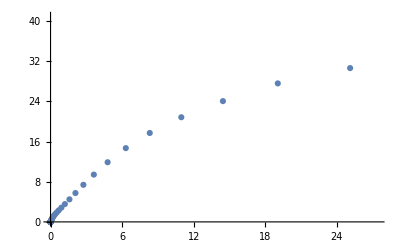

```mathematica
Inelastic
ListPlot[Elastic]
```

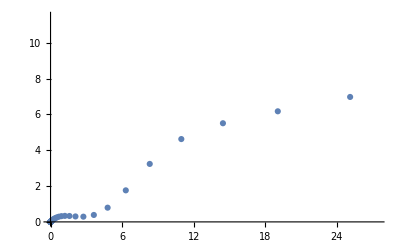

```mathematica
ListPlot[Inelastic]
```

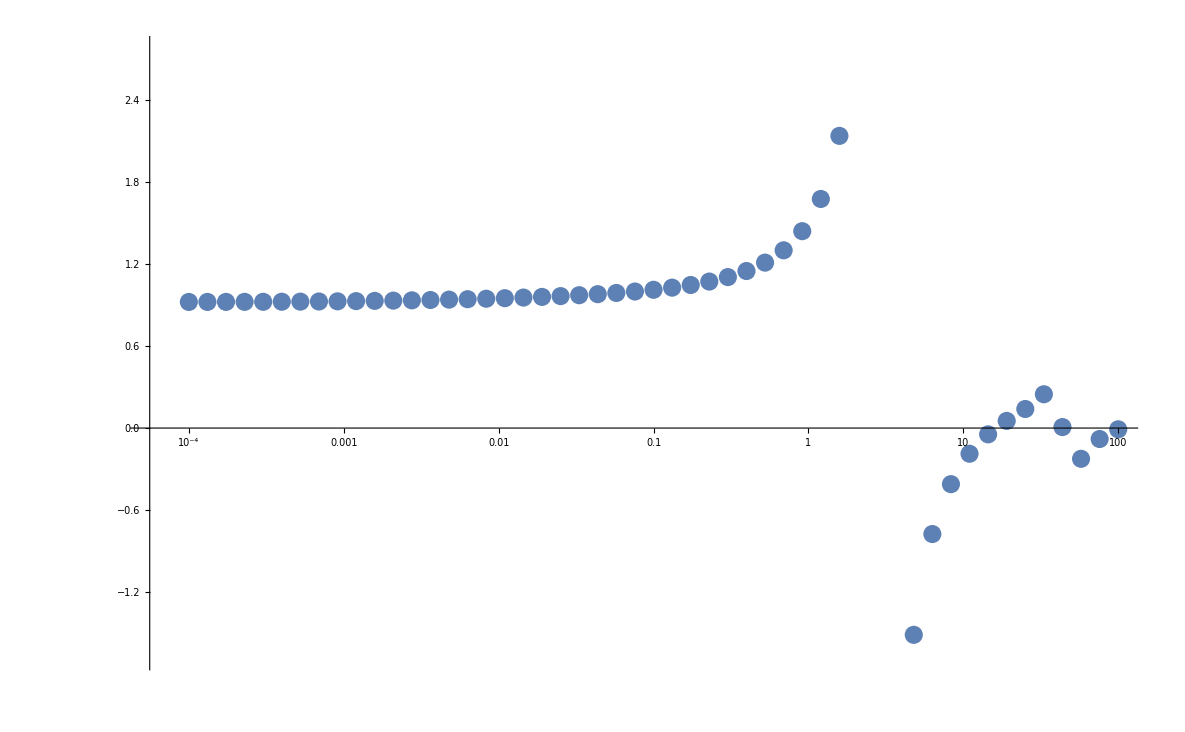

```mathematica
ListLogLinearPlot[Re[Sections]]
```

```mathematica
Re[Sections]
```

{{0.0001,0.922014},{0.000131826,0.922183},{0.00017378,0.922403},{0.000229087,0.922681},{0.000301995,0.923067},{0.000398107,0.923593},{0.000524807,0.924313},{0.000691831,0.925285},{0.000912011,0.926553},{0.00120226,0.928105},{0.00158489,0.929875},{0.0020893,0.931795},{0.00275423,0.933877},{0.00363078,0.936248},{0.0047863,0.939018},{0.00630957,0.942129},{0.00831764,0.945569},{0.0109648,0.949514},{0.0144544,0.953937},{0.0190546,0.958977},{0.0251189,0.964698},{0.0331131,0.971278},{0.0436516,0.978889},{0.057544,0.987787},{0.0758578,0.998328},{0.1,1.01102},{0.131826,1.02656},{0.17378,1.04597},{0.229087,1.07107},{0.301995,1.10378},{0.398107,1.14793},{0.524807,1.20959},{0.691831,1.29947},{0.912011,1.43938},{1.20226,1.6749},{1.58489,2.13628},{2.0893,3.36784},{2.75423,14.5737},{3.63078,-4.17746},{4.7863,-1.51183},{6.30957,-0.774968},{8.31764,-0.410221},{10.9648,-0.187836},{14.4544,-0.0459914},{19.0546,0.0523365},{25.1189,0.139363},{33.1131,0.247118},{43.6516,0.00715656},{57.544,-0.224868},{75.8578,-0.0802},{100.,-0.00907161}}

Imports

```mathematica
imported = Import["Drop_3D_30_07.csv"];
imported=Sort[imported,#1[[1]]<#2[[1]]&];
scat=Transpose[imported][[1]];
scat = (1/aHOz)*scat;
scat=1/scat;

energies=Transpose[imported][[2]];
energies = Ωz * energies;

colored = Join[Transpose[imported], {Range[Length[scat]]}];
```

```mathematica
Export["Before_scat_colored.csv",Transpose[colored]]
```

Before_scat_colored.csv

Calculations

```mathematica
Elastic={};Inelastic={}; Sections={};Scattered={}; Sections1D={};
en = 0.0000001;
Print["Progress:"];
Print[ProgressIndicator[Dynamic[k],{1,Length[scat]}]];
Do[aS=scat[[i]];
k=i;
(*Print["as = ",aS];*)

xi=0.25;
(*Determines the final point of integration*)
xf=100;

(* Subroutine determining steps *)
Module[{eig,h,dbl,n,pxi,pxf,dp,x,p,tab},

pxi=Log[xi ];
pxf=Log[xf +dxf];
dp=(pxf-pxi)/nptl;
tab=Table[x=Exp[p];eig=Eigenvalues[V[x]];{x,Min[2Pi/Sqrt[Abs[en-eig]]]},{p,pxi,pxf,dp}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,


AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
];
(*Print["nstep = ",nstep];*)
QT=Table[en Id-V[xt[[n]]],{n,1,Length[xt]}];
phi=φ/.Solve[aS==ash[φ],φ][[1]];
Kmatr=KMatrix[en,Sin[phi],Cos[phi]];
Smatr=(Id+ⅈ Kmatr).Inverse[Id-ⅈ Kmatr];
S0 = N[Smatr[[1,1]]];
a0 = 1/(ⅈ Sqrt[en])(1-S0)/(1+S0);

(*totinelS=Pi Sum[1-Abs[Smatr[[n1,n1]]]^2,{n1,1,1}]/en;
totelS=Pi Sum[Abs[1-Smatr[[n1,n1]]]^2,{n1,1,1}]/en;*)
(*Print[a0];*)
totInEl= Sum[(2TabCh[[n1,1]]+1)(1-Abs[Smatr[[n1,n1]]]^2),{n1,1,Nch}];
totEl=  Sum[(2TabCh[[n1,1]]+1)Abs[1-Smatr[[n1,n1]]]^2,{n1,1,Nch}];

AppendTo[Elastic,{en,totEl}];
AppendTo[Inelastic,{en,totInEl}];
AppendTo[Sections,Re[a0]];
AppendTo[Sections1D,i];
AppendTo[Scattered,{aS,Re[a0]}];

Clear[xt,QT];
,{i,1,Length[scat]}
]
```

Progress:

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00469568,0.,0.131772,0.,4.00454,0.,217.681,0.,13886.8,0.,«23»},{0.,-0.453516,0.,9.09329,0.,217.456,0.,10213.6,0.,584754.,«23»},{0.0000435028,0.,-72.182,0.,1318.46,0.,27979.5,0.,1.20826×10^6,0.,«23»},{0.,0.00060104,0.,-16055.4,0.,281353.,0.,5.54619×10^6,0.,2.2645×10^8,«23»},{3.74393×10^-8,0.,0.0373372,0.,-4.59063×10^6,0.,7.86629×10^7,0.,1.47315×10^9,0.,«23»},{0.,2.2612×10^-7,0.,4.42621,0.,-1.60417×10^9,0.,2.71294×10^10,0.,4.88951×10^11,«23»},{2.03744×10^-11,0.,7.93229×10^-6,0.,787.494,0.,-6.62484×10^11,0.,1.11152×10^13,0.,«23»},{0.,7.36091×10^-11,0.,0.00060472,0.,188024.,0.,-3.1568×10^14,0.,5.27155×10^15,«23»},{6.60621×10^-15,0.,1.74101×10^-9,0.,0.0749552,0.,5.64922×10^7,0.,-1.70481×10^17,0.,«23»},{0.,1.63796×10^-14,0.,9.59637×10^-8,0.,13.1707,0.,2.04882×10^10,0.,-1.02899×10^20,«23»},«23»} may contain significant numerical errors.

General::munfl: (1.28602×10^-160)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.73513×10^-167)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.00984×10^-173)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00469535,0.,0.131781,0.,4.00509,0.,217.719,0.,13889.7,0.,«23»},{0.,-0.453516,0.,9.09329,0.,217.456,0.,10213.6,0.,584754.,«23»},{0.0000435058,0.,-72.182,0.,1318.46,0.,27979.5,0.,1.20826×10^6,0.,«23»},{0.,0.00060104,0.,-16055.4,0.,281353.,0.,5.54619×10^6,0.,2.2645×10^8,«23»},{3.74443×10^-8,0.,0.0373372,0.,-4.59063×10^6,0.,7.86629×10^7,0.,1.47315×10^9,0.,«23»},{0.,2.2612×10^-7,0.,4.42621,0.,-1.60417×10^9,0.,2.71294×10^10,0.,4.88951×10^11,«23»},{2.03779×10^-11,0.,7.93229×10^-6,0.,787.494,0.,-6.62484×10^11,0.,1.11152×10^13,0.,«23»},{0.,7.36091×10^-11,0.,0.00060472,0.,188024.,0.,-3.1568×10^14,0.,5.27155×10^15,«23»},{6.60756×10^-15,0.,1.74101×10^-9,0.,0.0749552,0.,5.64922×10^7,0.,-1.70481×10^17,0.,«23»},{0.,1.63796×10^-14,0.,9.59637×10^-8,0.,13.1707,0.,2.04882×10^10,0.,-1.02899×10^20,«23»},«23»} may contain significant numerical errors.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00469502,0.,0.13179,0.,4.00563,0.,217.757,0.,13892.5,0.,«23»},{0.,-0.453516,0.,9.09329,0.,217.456,0.,10213.6,0.,584754.,«23»},{0.0000435088,0.,-72.182,0.,1318.46,0.,27979.5,0.,1.20826×10^6,0.,«23»},{0.,0.00060104,0.,-16055.4,0.,281353.,0.,5.54619×10^6,0.,2.2645×10^8,«23»},{3.74494×10^-8,0.,0.0373372,0.,-4.59063×10^6,0.,7.86629×10^7,0.,1.47315×10^9,0.,«23»},{0.,2.2612×10^-7,0.,4.42621,0.,-1.60417×10^9,0.,2.71294×10^10,0.,4.88951×10^11,«23»},{2.03815×10^-11,0.,7.93229×10^-6,0.,787.494,0.,-6.62484×10^11,0.,1.11152×10^13,0.,«23»},{0.,7.36091×10^-11,0.,0.00060472,0.,188024.,0.,-3.1568×10^14,0.,5.27155×10^15,«23»},{6.6089×10^-15,0.,1.74101×10^-9,0.,0.0749552,0.,5.64922×10^7,0.,-1.70481×10^17,0.,«23»},{0.,1.63796×10^-14,0.,9.59637×10^-8,0.,13.1707,0.,2.04882×10^10,0.,-1.02899×10^20,«23»},«23»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

```mathematica
Spectral=Join[{aHOz/Sections},{energies/Ωz}];
Spectral1=Join[{aHOz/Sections},{energies/Ωz},{Sections1D}];
Spectral1=Transpose[Spectral1];
Spectral=Transpose[Spectral];
Spectral
```

```mathematica
Export["Spectral_02.csv",Spectral];
Export["Spectral_colored.csv",Spectral1];
```

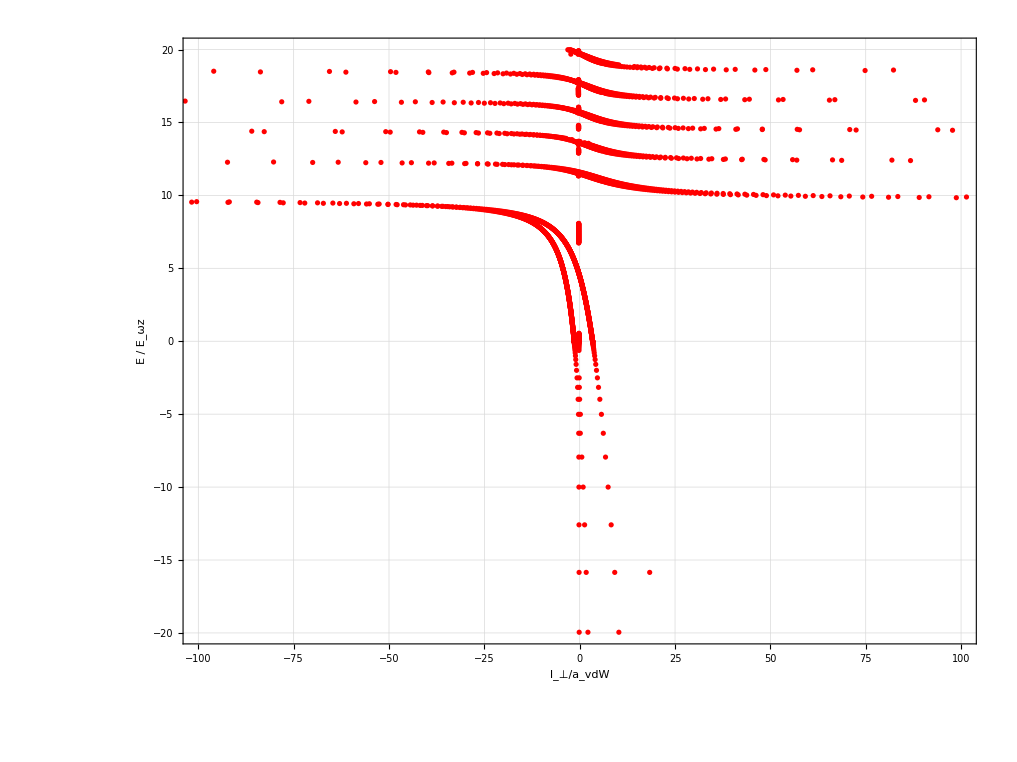

```mathematica
ListPlot[Re[Spectral],PlotRange->{{-100,100},All},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
Spectral
```

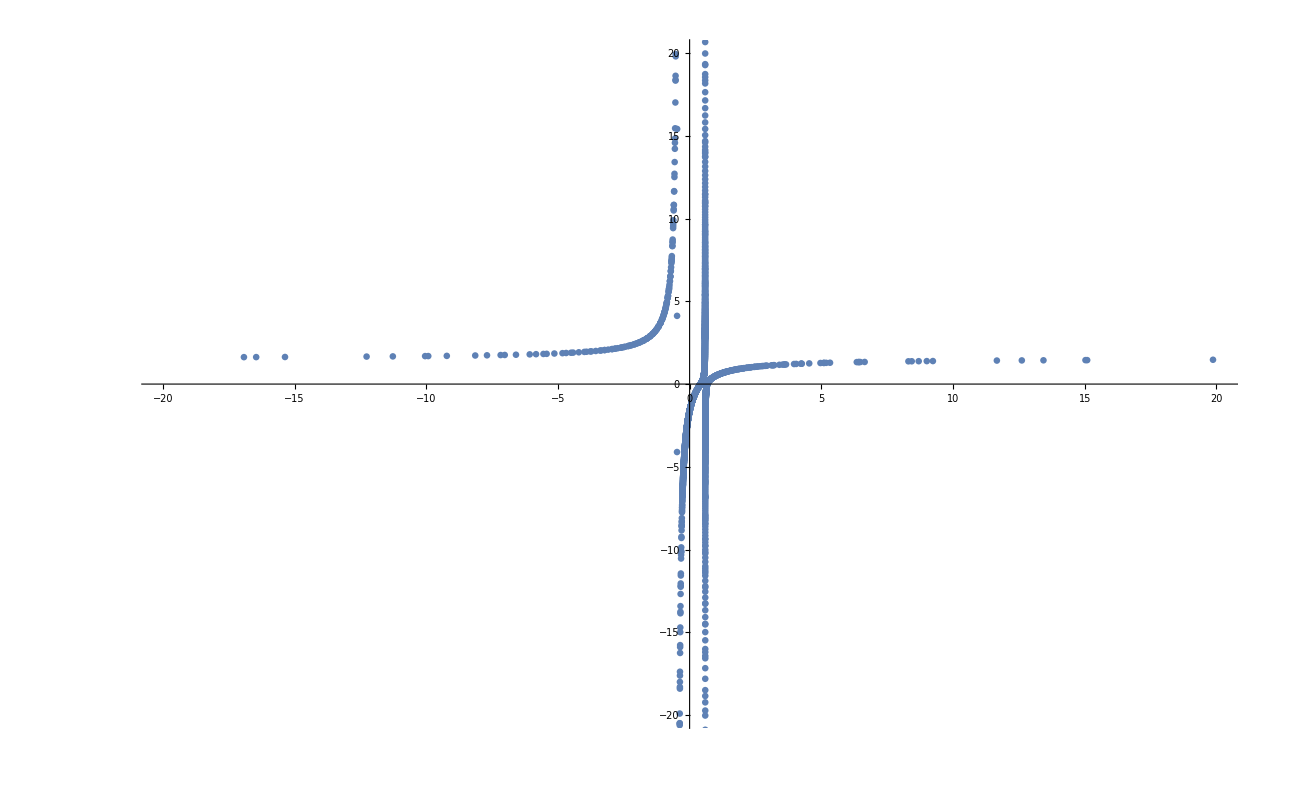

Scattered_02.csv

```mathematica
ListPlot[Re[Scattered], PlotRange->{{-20,20},{-20,20}}]
Export["Scattered_02.csv",Scattered]
```

```mathematica
Sections
```

{-1.62482,-1.63196,-1.63912,-1.64628,-1.64841,-1.65346,-1.66065,-1.66108,-1.66342,-1.66784,-1.67505,-1.68227,-1.6895,-1.69674,-1.704,-1.71126,-1.71854,-1.72421,-1.72583,-1.73313,-1.74044,-1.74776,-1.75509,-1.75551,-1.76244,-1.76917,-1.7698,-1.77105,-1.77717,-1.78456,-1.79195,-1.79936,-1.80678,-1.81422,-1.82167,-1.82913,-1.8366,-1.83725,-1.84409,-1.85159,-1.8591,-1.86663,-1.87,-1.87417,-1.88152,-1.88173,-1.8893,-1.89073,-1.89688,-1.90448,-1.91209,-1.91971,-1.92735,-1.93501,-1.94268,-1.95036,-1.95806,-1.95923,-1.96577,-1.9735,-1.98125,-1.98901,-1.99284,-1.99678,-2.00127,-2.00457,-2.01238,-2.0202,-2.02161,-2.02804,-2.03589,-2.04376,-2.05165,-2.05955,-2.06747,-2.0754,-2.08336,-2.09132,-2.09144,-2.09931,-2.10731,-2.11533,-2.12337,-2.12515,-2.12932,-2.13143,-2.1395,-2.14759,-2.15569,-2.16382,-2.16553,-2.17196,-2.18012,-2.1883,-2.1965,-2.20472,-2.21295,-2.22121,-2.22948,-2.23539,-2.23777,-2.24608,-2.25441,-2.26276,-2.26675,-2.26824,-2.27113,-2.27951,-2.28792,-2.29635,-2.3048,-2.31326,-2.32175,-2.32474,-2.33026,-2.33879,-2.34734,-2.3559,-2.3645,-2.37311,-2.38174,-2.39039,-2.39293,-2.39907,-2.40777,-2.41481,-2.41648,-2.42369,-2.42522,-2.43399,-2.44277,-2.45158,-2.46041,-2.46926,-2.47813,-2.48703,-2.49595,-2.50201,-2.50489,-2.51386,-2.52284,-2.53186,-2.54089,-2.54995,-2.55904,-2.5663,-2.56815,-2.57498,-2.57728,-2.58644,-2.59339,-2.59562,-2.60482,-2.61405,-2.62331,-2.63259,-2.6419,-2.65123,-2.66058,-2.66997,-2.67938,-2.68881,-2.69827,-2.70086,-2.70776,-2.71727,-2.72682,-2.73638,-2.74598,-2.74904,-2.7556,-2.75825,-2.76525,-2.77493,-2.77963,-2.78463,-2.79436,-2.80412,-2.81391,-2.82373,-2.83358,-2.84345,-2.85336,-2.86329,-2.87325,-2.88324,-2.89326,-2.90331,-2.91339,-2.92351,-2.92572,-2.93365,-2.9391,-2.94382,-2.95402,-2.96426,-2.97219,-2.97452,-2.98482,-2.9852,-2.99514,-3.0055,-3.0159,-3.02632,-3.03677,-3.04726,-3.05778,-3.06834,-3.07892,-3.08954,-3.1002,-3.11089,-3.12161,-3.13236,-3.14315,-3.14772,-3.15398,-3.16484,-3.17573,-3.18236,-3.18666,-3.19762,-3.20862,-3.21242,-3.21355,-3.21966,-3.23073,-3.24184,-3.25299,-3.26417,-3.27539,-3.28664,-3.29793,-3.30927,-3.32063,-3.33204,-3.34349,-3.35497,-3.36649,-3.37805,-3.37806,-3.38966,-3.4013,-3.41298,-3.4247,-3.43646,-3.44826,-3.4601,-3.46899,-3.47199,-3.47833,-3.48391,-3.48442,-3.49588,-3.50789,-3.51994,-3.53203,-3.54417,-3.55635,-3.56857,-3.58083,-3.59314,-3.6055,-3.61789,-3.63034,-3.63393,-3.64282,-3.65535,-3.66793,-3.68056,-3.69323,-3.70594,-3.7187,-3.73151,-3.74437,-3.75697,-3.75728,-3.77023,-3.78323,-3.79528,-3.79628,-3.80937,-3.82252,-3.82259,-3.82376,-3.83572,-3.84896,-3.86226,-3.87561,-3.889,-3.90245,-3.91595,-3.92018,-3.9295,-3.94311,-3.95676,-3.97047,-3.98423,-3.99805,-4.01192,-4.02584,-4.03982,-4.05385,-4.06794,-4.08209,-4.08447,-4.09629,-4.09958,-4.11054,-4.12486,-4.13923,-4.15365,-4.16814,-4.18268,-4.19729,-4.21195,-4.22667,-4.23253,-4.24145,-4.24288,-4.25629,-4.27119,-4.28616,-4.30118,-4.31627,-4.33142,-4.34663,-4.3619,-4.37724,-4.39265,-4.40811,-4.40856,-4.42365,-4.43924,-4.45491,-4.46057,-4.47064,-4.48643,-4.5023,-4.51823,-4.53423,-4.5503,-4.56644,-4.57408,-4.58265,-4.59892,-4.60978,-4.61527,-4.63169,-4.64818,-4.66475,-4.68138,-4.69809,-4.71487,-4.72412,-4.73173,-4.74866,-4.75569,-4.76567,-4.78275,-4.79991,-4.81715,-4.83446,-4.85185,-4.86932,-4.88687,-4.89728,-4.9045,-4.92221,-4.94,-4.95787,-4.97583,-4.99386,-5.01198,-5.03019,-5.03091,-5.04847,-5.06685,-5.08531,-5.10385,-5.12248,-5.1412,-5.14876,-5.16001,-5.17891,-5.19789,-5.21697,-5.23614,-5.2554,-5.27475,-5.29419,-5.31373,-5.32669,-5.33336,-5.35309,-5.37292,-5.39284,-5.41077,-5.41285,-5.43297,-5.45318,-5.4735,-5.49391,-5.51443,-5.51947,-5.53505,-5.55577,-5.57659,-5.59752,-5.59772,-5.61855,-5.63969,-5.66093,-5.67095,-5.68229,-5.70375,-5.72532,-5.747,-5.76879,-5.79069,-5.81271,-5.83484,-5.85708,-5.87944,-5.90191,-5.92451,-5.94722,-5.97005,-5.993,-6.01607,-6.02327,-6.03926,-6.06257,-6.08226,-6.08601,-6.09307,-6.10958,-6.11544,-6.13327,-6.15708,-6.18103,-6.2051,-6.22931,-6.25364,-6.27811,-6.30271,-6.32745,-6.35232,-6.37732,-6.40247,-6.40648,-6.42775,-6.45318,-6.47874,-6.50445,-6.5303,-6.55629,-6.58243,-6.58571,-6.58614,-6.58667,-6.58734,-6.58819,-6.58926,-6.5906,-6.59229,-6.59443,-6.59711,-6.60049,-6.60475,-6.61012,-6.61689,-6.62543,-6.63619,-6.64978,-6.66695,-6.68864,-6.7161,-6.71867,-6.7509,-6.76584,-6.77554,-6.79507,-6.85126,-6.92295,-7.01474,-7.05581,-7.13279,-7.28551,-7.32891,-7.42945,-7.48458,-7.59949,-7.68275,-7.74664,-8.09605,-8.27675,-8.35135,-8.51447,-8.56989,-8.60972,-8.83759,-9.22714,-9.29799,-9.86663,-10.0781,-10.1387,-10.1668,-10.3202,-10.539,-11.4454,-11.5656,-12.0476,-12.182,-12.2453,-12.6807,-13.4163,-13.7587,-13.8491,-14.7074,-14.9888,-15.7716,-15.8925,-16.2454,-17.3791,-17.6118,-17.9959,-18.2992,-18.401,-19.9064,-20.4883,-20.504,-20.6071,-21.4674,-21.7213,-22.4336,-22.6734,-22.8137,-23.2358,-23.5931,-24.1434,-24.2481,-25.9632,-26.5513,-27.1263,-27.9458,-28.0728,-28.5482,-28.8369,-28.8999,-28.9591,-29.008,-29.0149,-29.0676,-29.0788,-29.1177,-29.1654,-29.2109,-29.2545,-29.2963,-29.3365,-29.3703,-29.3752,-29.4127,-29.4489,-29.4841,-29.5182,-29.5514,-29.5838,-29.6154,-29.6462,-29.6633,-29.6764,-29.7061,-29.7351,-29.7637,-29.7832,-29.7918,-29.8194,-29.8467,-29.8736,-29.9002,-29.9264,-29.9524,-29.9782,-30.3016,-30.5878,-30.6986,-31.0128,-31.155,-31.1796,-31.204,-31.2283,-31.2525,-31.268,-31.2766,-31.3007,-31.3246,-31.3485,-31.3724,-31.3963,-31.4202,-31.4441,-31.4681,-31.48,-31.4921,-31.5162,-31.5404,-31.5673,-31.5991,-31.5996,-31.608,-31.6101,-31.651,-31.6659,-31.6904,-31.7283,-31.7372,-31.7648,-31.7827,-31.8001,-31.8143,-31.8343,-31.8675,-31.8981,-31.8998,-31.9312,-31.954,-31.9618,-31.9897,-31.9917,-31.9961,-32.0209,-32.0495,-32.0776,-32.0904,-32.1051,-32.1322,-32.2022,-32.2476,-32.3271,-32.3788,-32.468,-32.5493,-32.6287,-32.8142,-32.9132,-32.9184,-33.0312,-33.2892,-33.3811,-33.6019,-33.6056,-33.9788,-33.9897,-34.484,-34.5364,-34.7803,-35.1365,-35.8474,-35.9077,-36.0373,-36.2412,-36.2569,-36.2726,-36.2883,-36.304,-36.3198,-36.3355,-36.3513,-36.367,-36.3828,-36.3986,-36.4144,-36.4302,-36.446,-36.4619,-36.4777,-36.4936,-36.5095,-36.5254,-36.5413,-36.5572,-36.5731,-36.5891,-36.605,-36.621,-36.637,-36.653,-36.669,-36.685,-36.7011,-36.7171,-36.7332,-36.7493,-36.7654,-36.7815,-36.7976,-36.8138,-36.8299,-36.8461,-36.8623,-36.8785,-36.8947,-36.9109,-36.9272,-36.9435,-36.9597,-36.976,-36.9924,-37.0087,-37.025,-37.0398,-37.0414,-37.0578,-37.0742,-37.0906,-37.107,-37.1235,-37.14,-37.1564,-37.1729,-37.1895,-37.206,-37.2225,-37.2391,-37.2557,-37.2723,-37.2889,-37.3056,-37.3223,-37.3389,-37.3556,-37.3561,-37.3724,-37.3891,-37.4058,-37.4226,-37.4394,-37.4562,-37.4731,-37.4899,-37.5068,-37.5237,-37.5406,-37.5575,-37.5745,-37.5914,-37.5969,-37.6084,-37.8091,-39.4489,-40.3545,-40.9899,-42.3027,-43.174,-45.434,-46.7496,-47.2901,-47.7564,-47.8043,-47.8526,-47.9011,-47.9499,-47.9989,-48.0483,-48.0979,-48.1478,-48.198,-48.2485,-48.2994,-48.3505,-48.4019,-48.4536,-48.5056,-48.558,-48.6107,-48.6637,-48.717,-48.7707,-48.8247,-48.879,-48.9337,-48.9887,-49.0441,-49.0998,-49.1559,-49.2124,-49.2692,-49.3264,-49.384,-49.442,-49.5003,-49.5591,-49.5665,-49.5674,-49.5686,-49.5701,-49.5721,-49.5745,-49.5775,-49.5813,-49.5861,-49.5921,-49.5997,-49.6093,-49.6214,-49.6367,-49.6559,-49.6801,-49.7108,-49.7495,-49.7985,-49.8606,-49.9394,-50.0396,-50.1675,-50.3311,-50.5414,-50.8136,-51.0546,-51.1684,-51.636,-52.261,-52.9735,-53.3873,-56.6628,-59.0548,-60.5726,-61.6267,-72.3385,-72.9695,-73.5463,-83.8568,-91.8628,-95.2989,-101.949,-152.45,-243.06,-577.006,-782.589,-877.195,-1737.89,104.274,102.927,98.0429,82.0413,59.1282,52.2064,37.0874,29.2698,27.239,15.4119,4.12099,-4.10599,532.297,173.388,59.1752,43.2133,34.1736,34.1325,29.6201,27.1361,24.5434,19.9393,19.799,18.6252,18.3801,18.3361,17.0122,15.4531,14.8343,14.5764,14.2153,13.4127,12.7042,12.508,11.657,11.6308,10.8291,10.813,10.5609,10.4885,9.90055,9.70207,9.55288,9.42198,8.73205,8.61251,8.54668,8.35191,8.33191,7.73123,7.62456,7.50122,7.45275,7.391,7.30511,7.05589,6.84123,6.80755,6.50545,6.50543,6.48663,6.23028,6.20394,5.99968,5.86411,5.77474,5.74178,5.67467,5.58087,5.5779,5.33771,5.32255,5.22756,5.20863,5.19335,4.95841,4.89738,4.88228,4.84442,4.71932,4.63881,4.59147,4.52322,4.51207,4.40349,4.35576,4.33041,4.32511,4.22073,4.201,4.10303,4.09452,3.99186,3.96295,3.92033,3.88009,3.87577,3.73302,3.70622,3.68412,3.6734,3.67008,3.52642,3.50413,3.48282,3.45848,3.45425,3.33958,3.33807,3.31144,3.25824,3.24141,3.18421,3.1696,3.15384,3.08171,3.0495,3.04111,3.01413,3.00825,2.92173,2.90754,2.87848,2.8732,2.87124,2.78244,2.77593,2.74746,2.73932,2.72503,2.6649,2.64236,2.62997,2.61702,2.58645,2.55414,2.51981,2.51943,2.5032,2.46061,2.44948,2.41622,2.4058,2.39689,2.35032,2.34574,2.31851,2.30034,2.29727,2.25613,2.2404,2.22609,2.20362,2.20211,2.16647,2.14338,2.13846,2.11534,2.11029,2.0809,2.05516,2.05369,2.03187,2.0242,1.99909,1.97579,1.97046,1.95275,1.94322,1.92068,1.89999,1.89297,1.87758,1.86685,1.84541,1.82746,1.8206,1.80598,1.79462,1.77299,1.7579,1.75283,1.73763,1.72614,1.70321,1.69107,1.68918,1.67225,1.66107,1.63584,1.62926,1.62673,1.60958,1.59909,1.57272,1.5707,1.49148,1.48335,1.46858,1.44676,1.44638,1.43566,1.42912,1.42047,1.39055,1.38689,1.38176,1.37706,1.3747,1.33599,1.33109,1.32963,1.32902,1.32698,1.28947,1.28294,1.27913,1.27873,1.27261,1.24967,1.23217,1.2313,1.23013,1.21758,1.21158,1.18716,1.18251,1.18094,1.17506,1.1638,1.14359,1.13999,1.13618,1.13177,1.11118,1.10629,1.10135,1.09102,1.0837,1.07386,1.06033,1.05963,1.04696,1.04261,1.03664,1.02046,1.01248,1.00907,1.00391,0.990516,0.983374,0.981632,0.961786,0.959415,0.955247,0.945248,0.943783,0.928036,0.920521,0.910599,0.90684,0.901685,0.900769,0.880048,0.876147,0.870735,0.862554,0.857016,0.851374,0.840304,0.835408,0.827323,0.815221,0.81393,0.803957,0.801232,0.8008,0.781238,0.771455,0.768543,0.766858,0.762777,0.759132,0.737608,0.733534,0.729541,0.724889,0.722472,0.716636,0.700779,0.69619,0.688142,0.687521,0.676964,0.676243,0.66855,0.656773,0.650629,0.647215,0.637755,0.636805,0.631981,0.619171,0.614172,0.606722,0.605508,0.601,0.587493,0.583223,0.578114,0.57462,0.56663,0.565825,0.548788,0.54411,0.54348,0.542423,0.532106,0.526943,0.51896,0.515694,0.513905,0.507033,0.499886,0.499657,0.48753,0.484067,0.483941,0.471984,0.468491,0.456791,0.454485,0.453323,0.448479,0.438424,0.437193,0.425154,0.423783,0.414118,0.40974,0.40939,0.402649,0.396045,0.395235,0.38131,0.371893,0.371294,0.368326,0.367605,0.367128,0.354112,0.340822,0.338375,0.334197,0.333128,0.330117,0.327727,0.314819,0.309753,0.302092,0.300234,0.295221,0.289538,0.288787,0.281229,0.277149,0.266401,0.264919,0.257547,0.252842,0.252767,0.247888,0.24091,0.232657,0.229118,0.224325,0.220068,0.217459,0.207382,0.205927,0.198953,0.19586,0.194518,0.183224,0.182727,0.172041,0.167321,0.167208,0.165227,0.160964,0.149988,0.145455,0.139107,0.138654,0.131412,0.128316,0.127278,0.117613,0.1098,0.108164,0.106991,0.0974278,0.0964469,0.087486,0.0859767,0.0806951,0.0755764,0.0707571,0.0652422,0.0631887,0.0549707,0.0512737,0.0477106,0.0447583,0.0346017,0.0331254,0.0286036,0.0244979,0.0214655,0.0144438,0.00782459,0.0044365,-0.00484241,-0.00552678,-0.00642294,-0.0088025,-0.0154487,-0.0253318,-0.0323006,-0.0351786,-0.039606,-0.0419889,-0.0432606,-0.0449913,-0.0547724,-0.0645239,-0.0710242,-0.0727917,-0.074248,-0.0781949,-0.0822443,-0.0839466,-0.0936218,-0.103139,-0.103275,-0.112909,-0.113772,-0.115144,-0.121909,-0.122525,-0.132125,-0.136039,-0.14171,-0.151281,-0.152944,-0.155363,-0.160842,-0.162371,-0.169814,-0.170392,-0.179934,-0.189469,-0.191704,-0.197683,-0.198998,-0.203749,-0.204562,-0.208522,-0.218044,-0.227564,-0.231542,-0.237083,-0.240389,-0.240852,-0.246166,-0.246603,-0.256125,-0.265651,-0.272581,-0.27518,-0.277408,-0.284715,-0.28499,-0.289749,-0.294257,-0.303806,-0.313365,-0.314953,-0.315742,-0.322933,-0.330221,-0.332512,-0.334634,-0.342103,-0.351707,-0.355526,-0.358801,-0.361325,-0.370958,-0.376676,-0.380607,-0.380963,-0.390274,-0.396909,-0.399958,-0.40428,-0.409661,-0.419385,-0.424491,-0.428893,-0.429129,-0.438895,-0.440056,-0.448685,-0.451561,-0.458498,-0.468335,-0.473813,-0.478199,-0.478592,-0.485149,-0.488089,-0.498007,-0.500832,-0.507953,-0.517929,-0.5248,-0.527935,-0.530245,-0.532396,-0.537972,-0.548042,-0.552303,-0.558145,-0.568282,-0.577625,-0.578454,-0.582026,-0.584055,-0.588662,-0.598907,-0.606205,-0.609189,-0.619511,-0.629872,-0.632474,-0.634301,-0.640248,-0.640274,-0.650718,-0.661205,-0.662803,-0.671735,-0.682309,-0.689518,-0.689557,-0.69293,-0.699078,-0.703596,-0.71431,-0.722391,-0.725073,-0.735885,-0.746748,-0.748017,-0.749102,-0.757663,-0.760828,-0.76863,-0.77965,-0.785307,-0.790725,-0.801856,-0.810187,-0.811367,-0.813044,-0.82429,-0.825818,-0.835594,-0.846959,-0.851935,-0.858385,-0.869873,-0.876481,-0.876638,-0.881424,-0.89304,-0.894412,-0.904722,-0.916471,-0.922716,-0.928287,-0.940174,-0.945239,-0.94742,-0.95213,-0.964158,-0.967024,-0.97626,-0.988435,-0.99816,-1.00069,-1.01301,-1.01754,-1.02362,-1.02542,-1.03791,-1.04413,-1.05047,-1.06312,-1.07585,-1.07886,-1.08867,-1.09395,-1.10157,-1.1058,-1.11457,-1.12628,-1.12765,-1.14082,-1.15408,-1.1655,-1.16744,-1.17495,-1.18089,-1.19444,-1.19482,-1.20809,-1.21411,-1.22184,-1.2357,-1.24965,-1.25891,-1.2611,-1.26371,-1.27788,-1.29171,-1.29216,-1.30655,-1.30837,-1.32105,-1.33567,-1.3504,-1.35301,-1.36005,-1.36525,-1.38022,-1.39532,-1.3977,-1.40993,-1.41053,-1.42588,-1.44135,-1.45144,-1.45696,-1.47007,-1.4727,-1.48857,-1.50459,-1.5143,-1.51983,-1.52074,-1.53703,-1.55348,-1.55726,-1.57006,-1.5868,-1.59038,-1.60369,-1.62074,-1.63794,-1.63931,-1.64337,-1.65531,-1.67147,-1.67284,-1.69054,-1.7084,-1.72265,-1.72644,-1.74465,-1.76305,-1.76987,-1.78162,-1.7872,-1.7953,-1.80038,-1.81933,-1.83847,-1.85781,-1.869,-1.87735,-1.89709,-1.91332,-1.91703,-1.93019,-1.93719,-1.94872,-1.95756,-1.97815,-1.99896,-2.02,-2.032,-2.04127,-2.06277,-2.07189,-2.07792,-2.08452,-2.10651,-2.12875,-2.13166,-2.15124,-2.17399,-2.19701,-2.21495,-2.2203,-2.24062,-2.24386,-2.24837,-2.2677,-2.29183,-2.31625,-2.34085,-2.34097,-2.36599,-2.39132,-2.41697,-2.42093,-2.42201,-2.44294,-2.44623,-2.46924,-2.49588,-2.52286,-2.55019,-2.57789,-2.58272,-2.60595,-2.62218,-2.63438,-2.65864,-2.6632,-2.66993,-2.69241,-2.72202,-2.75204,-2.78247,-2.81334,-2.84464,-2.84852,-2.86596,-2.87639,-2.90859,-2.92524,-2.94127,-2.97443,-3.00807,-3.04222,-3.06781,-3.07689,-3.10534,-3.11208,-3.14781,-3.18409,-3.20265,-3.2198,-3.22094,-3.25838,-3.2964,-3.3234,-3.33504,-3.37431,-3.39962,-3.41422,-3.45478,-3.49603,-3.53797,-3.56387,-3.58062,-3.61003,-3.61412,-3.624,-3.66814,-3.71305,-3.74068,-3.75875,-3.80526,-3.85262,-3.90084,-3.94818,-3.94995,-3.97169,-3.99996,-4.05092,-4.10285,-4.11369,-4.14121,-4.15577,-4.20972,-4.26472,-4.32081,-4.33659,-4.37803,-4.4364,-4.46348,-4.49597,-4.55677,-4.61884,-4.6189,-4.65814,-4.68222,-4.74696,-4.75323,-4.79437,-4.8131,-4.8807,-4.94978,-5.02042,-5.069,-5.09266,-5.16657,-5.19924,-5.24219,-5.31959,-5.34269,-5.39883,-5.47999,-5.56313,-5.59336,-5.64834,-5.73568,-5.82525,-5.83399,-5.91712,-5.92033,-6.01139,-6.01226,-6.10816,-6.20753,-6.30961,-6.41451,-6.52235,-6.63326,-6.74737,-6.7477,-6.83247,-6.84175,-6.84942,-6.86482,-6.98577,-7.11038,-7.23881,-7.37125,-7.50789,-7.64894,-7.7946,-7.9276,-7.94512,-8.06224,-8.10075,-8.19264,-8.26175,-8.4284,-8.43551,-8.60101,-8.77992,-8.96547,-9.15804,-9.35803,-9.37043,-9.56591,-9.75815,-9.78213,-10.0072,-10.1575,-10.2417,-10.4863,-10.7415,-11.0081,-11.1419,-11.287,-11.4035,-11.5789,-11.8848,-12.2058,-12.2783,-12.5429,-12.8975,-13.2508,-13.2709,-13.6647,-14.0806,-14.4867,-14.5205,-14.9866,-15.4812,-16.0072,-16.1961,-16.4235,-16.5676,-17.1658,-17.8058,-18.4923,-18.8458,-19.2304,-19.7254,-20.0262,-20.8868,-21.8204,-22.8368,-23.9474,-24.5279,-25.1661,-26.5093,-27.9973,-29.0189,-29.6549,-30.615,-31.5127,-31.915,-32.0658,-33.6094,-35.9942,-38.7311,-41.9042,-45.6268,-47.5038,-50.0553,-55.4115,-62.0211,-67.0973,-70.3826,-81.2989,-96.1521,-102.115,-117.541,-126.825,-127.489,-150.996,-210.742,-347.824,-589.543,-987.923,1185.83,383.054,371.528,220.618,157.066,122.044,99.8626,89.6185,84.5534,73.3512,66.4804,64.7986,58.0549,57.7118,55.0675,52.6012,50.2395,48.0995,44.3205,41.1032,38.3309,35.9172,33.7969,31.9193,31.5388,30.2452,28.7431,27.7383,27.3878,27.0252,26.1587,25.0391,24.0149,23.0743,22.9362,22.2076,21.4064,20.6634,19.9727,19.3288,19.2719,18.7271,18.5434,18.3471,18.1636,17.6349,17.1376,16.6692,16.2272,15.8094,15.4139,15.0389,14.6828,14.5942,14.3444,14.144,14.0222,13.9395,13.7522,13.7152,13.4222,13.1424,12.8749,12.6189,12.3736,12.1385,11.9128,11.696,11.4877,11.4487,11.2872,11.0942,11.0241,10.9543,10.9083,10.7566,10.7291,10.5562,10.3893,10.228,10.0722,9.92153,9.77572,9.63456,9.6263,9.49783,9.36532,9.23683,9.21542,9.1122,9.04425,8.99124,8.87379,8.75971,8.64885,8.54878,8.54107,8.43625,8.33427,8.31051,8.235,8.13836,8.10939,8.04422,7.9525,7.92702,7.8631,7.77593,7.71571,7.69092,7.60798,7.52703,7.44801,7.37085,7.31485,7.29547,7.22183,7.14986,7.1131,7.0795,7.0107,6.96162,6.9468,6.9434,6.87757,6.81315,6.75009,6.73718,6.68835,6.6279,6.56869,6.53434,6.51068,6.45383,6.39812,6.3435,6.28995,6.23744,6.21049,6.18593,6.13539,6.10386,6.0858,6.08552,6.03713,5.98936,5.98564,5.94245,5.90539,5.8964,5.85116,5.80673,5.76308,5.72019,5.67804,5.6366,5.60877,5.59587,5.55583,5.51645,5.47772,5.43962,5.42113,5.40214,5.38965,5.38722,5.36527,5.35495,5.32898,5.29327,5.25812,5.22352,5.18945,5.1559,5.12287,5.11537,5.09033,5.05828,5.0267,4.99559,4.96493,4.95245,4.93472,4.90495,4.90493,4.89249,4.8756,4.84666,4.81813,4.79001,4.77661,4.76227,4.73491,4.70793,4.70301,4.68132,4.65506,4.62916,4.6036,4.58206,4.57838,4.55348,4.52892,4.50467,4.50253,4.48073,4.46138,4.4571,4.43376,4.41072,4.38797,4.3655,4.35285,4.34331,4.32139,4.31611,4.29974,4.27835,4.26239,4.25722,4.23634,4.21571,4.19532,4.17517,4.16274,4.15526,4.13557,4.11611,4.10271,4.09688,4.07786,4.05906,4.05146,4.04047,4.02209,4.00392,3.98594,3.98339,3.96816,3.95058,3.94041,3.93318,3.91597,3.89895,3.88211,3.87168,3.86545,3.84896,3.83265,3.8165,3.80053,3.7993,3.78904,3.78472,3.76907,3.75358,3.73824,3.73748,3.72307,3.70804,3.69317,3.67844,3.66385,3.64941,3.63512,3.62778,3.62096,3.61928,3.60693,3.59305,3.57929,3.56567,3.55822,3.55217,3.53901,3.5388,3.52556,3.51888,3.51244,3.49945,3.48657,3.47381,3.46117,3.44864,3.43623,3.42392,3.41173,3.39965,3.39808,3.38767,3.3758,3.36404,3.36333,3.35338,3.35237,3.34081,3.32935,3.32306,3.31799,3.31302,3.30672,3.29556,3.28448,3.2735,3.26262,3.25182,3.24112,3.2305,3.21997,3.20953,3.2024,3.19917,3.1889,3.17871,3.17018,3.16861,3.15858,3.14864,3.14644,3.13877,3.1365,3.12899,3.11928,3.11474,3.10965,3.10009,3.09061,3.0812,3.07186,3.0626,3.05341,3.04429,3.03524,3.02788,3.02625,3.01734,3.00849,3.00516,2.9997,2.99099,2.98615,2.98234,2.97375,2.96522,2.95676,2.94836,2.94002,2.93964,2.93919,2.93174,2.92352,2.91536,2.90726,2.89922,2.89123,2.8833,2.87543,2.87108,2.86761,2.85984,2.85559,2.85213,2.84448,2.83987,2.83687,2.82932,2.82182,2.81438,2.81345,2.81333,2.81318,2.81299,2.81275,2.81245,2.81207,2.81159,2.81099,2.81024,2.80929,2.80809,2.80659,2.8047,2.80233,2.79935,2.79561,2.79092,2.78504,2.7825,2.77769,2.76851,2.767,2.75706,2.74282,2.72927,2.72516,2.71922,2.70568,2.70335,2.67652,2.64372,2.64163,2.61426,2.60389,2.60025,2.59425,2.582,2.55591,2.51416,2.49869,2.48224,2.47918,2.47803,2.46753,2.43124,2.39814,2.37376,2.37274,2.36115,2.35568,2.35283,2.29198,2.2739,2.27358,2.26308,2.26192,2.24509,2.19437,2.18176,2.18069,2.16903,2.16213,2.14456,2.10422,2.09556,2.09422,2.0818,2.05269,2.05078,2.02061,2.01465,2.01343,1.99964,1.96836,1.94277,1.93848,1.93769,1.93046,1.92202,1.8906,1.87005,1.86655,1.86647,1.84849,1.81862,1.80325,1.80189,1.79929,1.79844,1.77866,1.75174,1.73779,1.73575,1.73378,1.71218,1.68939,1.67735,1.6755,1.67225,1.67164,1.64874,1.63109,1.6202,1.6182,1.61354,1.58806,1.57641,1.56601,1.5636,1.55741,1.53837,1.5299,1.52499,1.51451,1.51145,1.50363,1.4765,1.47403,1.46545,1.46152,1.45198,1.43068,1.42027,1.41861,1.41363,1.40611,1.4023,1.38727,1.3738,1.36843,1.36759,1.3544,1.34606,1.33084,1.32325,1.31836,1.30814,1.30687,1.28957,1.28047,1.27722,1.26989,1.26952,1.26339,1.24986,1.23912,1.23387,1.22291,1.22001,1.21157,1.19977,1.19908,1.1779,1.17728,1.1746,1.16711,1.16025,1.15363,1.13883,1.13695,1.13578,1.13289,1.12252,1.10568,1.10417,1.09706,1.08965,1.0858,1.07673,1.07053,1.05815,1.05003,1.04884,1.04744,1.03785,1.0367,1.02193,1.02012,1.0151,1.00619,1.00603,0.99595,0.982915,0.980966,0.975009,0.970831,0.965801,0.947546,0.946518,0.946448,0.944732,0.927272,0.926203,0.92296,0.915136,0.914783,0.910656,0.90011,0.886166,0.882617,0.877925,0.875473,0.857772,0.856366,0.850993,0.840839,0.835396,0.829906,0.819858,0.81498,0.806696,0.802522,0.795088,0.789163,0.77569,0.775578,0.772987,0.75886,0.756758,0.749033,0.73966,0.738269,0.728903,0.722849,0.720197,0.70666,0.702521,0.699247,0.696989,0.685221,0.673936,0.671417,0.669848,0.668277,0.665199,0.651671,0.646099,0.641438,0.640665,0.635387,0.629453,0.621001,0.619408,0.611654,0.609114,0.60372,0.596091,0.593905,0.588309,0.582775,0.576913,0.573161,0.571337,0.558494,0.558264,0.553984,0.546707,0.544782,0.543606,0.529177,0.525241,0.523153,0.52217,0.514965,0.512668,0.50096,0.497694,0.496501,0.487813,0.487155,0.480514,0.473539,0.473249,0.467721,0.460104,0.452402,0.448803,0.448263,0.446842,0.438855,0.433746,0.424324,0.420809,0.41684,0.415851,0.409855,0.408023,0.39978,0.395383,0.383214,0.382883,0.381043,0.380673,0.375139,0.370517,0.358279,0.351259,0.350369,0.350283,0.346165,0.344919,0.33417,0.325435,0.322289,0.321561,0.316983,0.310518,0.30837,0.300305,0.298854,0.291524,0.287293,0.28324,0.27583,0.274947,0.271294,0.264464,0.261097,0.253192,0.249328,0.248977,0.24201,0.233586,0.230916,0.230228,0.223419,0.219909,0.214119,0.208985,0.198868,0.198143,0.197191,0.195149,0.187382,0.178599,0.176699,0.170618,0.166975,0.166094,0.155895,0.155564,0.145109,0.143675,0.142358,0.134727,0.13451,0.124418,0.116342,0.115754,0.11418,0.10535,0.104012,0.101443,0.0939142,0.0885985,0.0838844,0.0746808,0.0739222,0.0677495,0.0675412,0.0640267,0.0604271,0.054197,0.0444323,0.0347318,0.0334103,0.0326485,0.03181,0.0289095,0.0250945,0.0155196,0.00600618,0.0027292,-0.00159234,-0.00344652,-0.0103519,-0.0105598,-0.0128394,-0.0221734,-0.026835,-0.0314494,-0.0372757,-0.0406683,-0.0498309,-0.0508788,-0.0543208,-0.0569044,-0.0589382,-0.0679911,-0.0736595,-0.0769904,-0.0859371,-0.0875043,-0.0920612,-0.094832,-0.0992576,-0.103676,-0.110768,-0.11247,-0.118663,-0.121215,-0.129912,-0.134126,-0.138562,-0.145167,-0.147165,-0.14863,-0.150414,-0.155723,-0.164236,-0.172705,-0.1771,-0.18113,-0.182794,-0.187282,-0.189514,-0.192062,-0.197856,-0.206158,-0.21442,-0.215845,-0.221017,-0.222643,-0.226767,-0.230827,-0.238974,-0.239969,-0.247084,-0.249615,-0.255158,-0.263197,-0.265925,-0.267135,-0.271201,-0.279171,-0.284156,-0.287108,-0.288924,-0.295012,-0.302885,-0.308445,-0.310726,-0.311876,-0.318536,-0.319526,-0.326316,-0.334067,-0.338977,-0.341789,-0.349483,-0.350761,-0.35579,-0.357149,-0.358937,-0.364788,-0.372401,-0.379987,-0.387549,-0.39019,-0.393019,-0.394159,-0.395085,-0.402597,-0.407182,-0.410085,-0.417549,-0.424991,-0.431291,-0.43241,-0.438721,-0.439807,-0.442635,-0.447183,-0.454538,-0.456697,-0.461872,-0.469186,-0.470692,-0.476481,-0.483756,-0.484538,-0.491012,-0.496399,-0.49825,-0.505469,-0.507579,-0.511318,-0.512671,-0.519856,-0.527024,-0.531714,-0.534176,-0.541311,-0.54843,-0.551577,-0.553273,-0.555534,-0.559934,-0.562623,-0.569698,-0.576757,-0.580361,-0.583803,-0.590835,-0.596673,-0.597854,-0.604859,-0.60828,-0.611852,-0.613884,-0.618832,-0.625801,-0.630605,-0.632757,-0.639701,-0.641646,-0.646635,-0.653557,-0.660469,-0.666628,-0.66737,-0.669561,-0.674261,-0.681142,-0.682583,-0.688013,-0.688336,-0.694875,-0.701728,-0.708572,-0.715407,-0.722234,-0.726757,-0.727114,-0.729052,-0.735863,-0.736451,-0.736898,-0.742666,-0.749462,-0.75625,-0.763032,-0.769806,-0.776574,-0.783336,-0.786706,-0.78751,-0.788818,-0.790092,-0.792377,-0.796841,-0.803585,-0.810324,-0.817057,-0.823785,-0.830508,-0.837227,-0.840369,-0.84394,-0.848521,-0.850552,-0.85065,-0.852978,-0.857356,-0.864057,-0.870755,-0.877449,-0.88414,-0.890827,-0.895696,-0.897512,-0.904193,-0.910872,-0.911189,-0.91276,-0.917548,-0.919421,-0.924222,-0.930894,-0.937564,-0.944232,-0.950898,-0.953739,-0.957563,-0.964226,-0.970888,-0.974524,-0.977549,-0.97965,-0.984209,-0.988352,-0.990868,-0.997527,-1.00419,-1.01084,-1.01478,-1.0175,-1.02416,-1.03082,-1.03747,-1.04082,-1.04413,-1.04944,-1.05079,-1.05745,-1.06,-1.06411,-1.07077,-1.07744,-1.07914,-1.0841,-1.09077,-1.09743,-1.1041,-1.11039,-1.11077,-1.11744,-1.12243,-1.12412,-1.1308,-1.13462,-1.13747,-1.14415,-1.14717,-1.15084,-1.15753,-1.16421,-1.17091,-1.1776,-1.18356,-1.1843,-1.191,-1.19771,-1.19891,-1.20442,-1.21113,-1.2125,-1.21784,-1.2193,-1.22456,-1.23129,-1.23802,-1.24475,-1.25148,-1.25823,-1.26071,-1.26497,-1.27172,-1.27848,-1.27927,-1.28524,-1.292,-1.29395,-1.29601,-1.29877,-1.30555,-1.31233,-1.31912,-1.32591,-1.33271,-1.33951,-1.3423,-1.34632,-1.35314,-1.35996,-1.3639,-1.36679,-1.37362,-1.37784,-1.37933,-1.38046,-1.38731,-1.39417,-1.40103,-1.4079,-1.41477,-1.42165,-1.42854,-1.42881,-1.43544,-1.44234,-1.44926,-1.45326,-1.45618,-1.4631,-1.46544,-1.46906,-1.47004,-1.47698,-1.48393,-1.49089,-1.49786,-1.50484,-1.51182,-1.51881,-1.52084,-1.52582,-1.53283,-1.53985,-1.54688,-1.5479,-1.55391,-1.55956,-1.56096,-1.56358,-1.56802,-1.57508,-1.58216,-1.58924,-1.59634,-1.60344,-1.61056,-1.61768,-1.61905}